# Game Theory Project

## June 24, 2018 - July 13, 2018

## Poly-matrix Games

```mathematica
Get[NotebookDirectory[]<>"\\Packages\\GameTheory.wl"]
```

```mathematica
(* 2 player games: MaxMin - pure strategies, Nash Equilibrium - pure and mixed strategies, Stackelberg Equilibrium - pure strategies ??? *)
```

```mathematica
Clear[a,b]
a={{2,2,3},{7,2,2},{1,1,4}};
b={{5,6,1},{5,2,3},{3,5,7}}; 
(*Clear[a,b]
a=RandomInteger[{-120,120},{50,50}];
b=RandomInteger[{-120,120},{50,50}];*)
MatrixForm/@{a,b}
```

{(2 | 2 | 3
7 | 2 | 2
1 | 1 | 4),(5 | 6 | 1
5 | 2 | 3
3 | 5 | 7)}

```mathematica
Clear[a,b]
a={{-1,-3},{0,-2}};
b={{-1,0},{-3,-2}}; 
(*Clear[a,b]
a=RandomInteger[{-120,120},{50,50}];
b=RandomInteger[{-120,120},{50,50}];*)
MatrixForm/@{a,b}
```

{(-1 | -3
0 | -2),(-1 | 0
-3 | -2)}

```mathematica
GameTheory[{a,b},Method->{"Criteria"->"Maximize","Concept"->"MaxMin","Strategy"->"Pure"}]
```

{Player 1→<|Strategy→{1,2},Payoff→2|>,Player 2→<|Strategy→{1},Payoff→3|>}

```mathematica
GameTheory[{a,b},Method->{"Criteria"->"Maximize","Concept"->"NashEquilibrium","Strategy"->"Pure"}]
```

{<|Player 1→1,Player 2→2|>→{2,6},<|Player 1→2,Player 2→1|>→{7,5},<|Player 1→3,Player 2→3|>→{4,7}}

```mathematica
GameTheory[{a,b},Method->{"Criteria"->"Maximize","Concept"->"NashEquilibrium","Strategy"->"Mixed"}]
```

{{{{x1→1,x2→0,x3→0}},{{y1→0,y2→1,y3→0}}},{{{x1→3/4,x2→1/4,x3→0}},{{y1→0,y2→1,y3→0}}},{{{x1→ConditionalExpression[1-x2,0≤x2≤1/4],x3→ConditionalExpression[0,0≤x2≤1/4]}},{{y1→0,y2→1,y3→0}}},{{{x1→2/7,x2→0,x3→5/7}},{{y1→0,y2→1/2,y3→1/2}}},{{{x1→4/17,x2→6/17,x3→7/17}},{{y1→1/10,y2→2/5,y3→1/2}}},{{{x1→0,x2→1,x3→0}},{{y1→1,y2→0,y3→0}}},{{{x1→0,x2→2/3,x3→1/3}},{{y1→1/4,y2→0,y3→3/4}}},{{{x1→0,x2→0,x3→1}},{{y1→0,y2→0,y3→1}}}}

```mathematica
GameTheory[{a,b},Method->{"Criteria"->"Maximize","Concept"->"StackelbergEquilibrium","Strategy"->"Pure"}]
```

```mathematica
(* 2 player game Plot *)
```

```mathematica
Clear[a,b]
a={{5,3},{7,2}};
b={{3,6},{5,3}}; 
MatrixForm/@{a,b}
```

{(5 | 3
7 | 2),(3 | 6
5 | 3)}

```mathematica
{({{5, 3}, {7, 2}}),({{3, 6}, {5, 3}})}
```

{{{5,3},{7,2}},{{3,6},{5,3}}}

```mathematica
GameTheoryPlot[{a,b}]
```

```mathematica
Clear[a,b]
a={{-1,-3},{0,-2}};
b={{-1,0},{-3,-2}}; 
(*Clear[a,b]
a=RandomInteger[{-120,120},{50,50}];
b=RandomInteger[{-120,120},{50,50}];*)
MatrixForm/@{a,b}
```

{(-1 | -3
0 | -2),(-1 | 0
-3 | -2)}

```mathematica
GameTheoryPlot[{a,b}]
```

----------------------------------------------------------------------- 3 player game ---------------------------------------------------------------

```mathematica
Clear[a,b,c]
a=RandomInteger[{-10,10},{5,5,5}];
b=RandomInteger[{-10,10},{5,5,5}];
c=RandomInteger[{-10,10},{5,5,5}];
MatrixForm/@{a,b,c};
```

```mathematica
GameTheory[{a,b},Method->{"Criteria"->"Maximize","Concept"->"MaxMin","Strategy"->"Pure"}]
```

{Player 1→<|Strategy→{2},Payoff→-2|>,Player 2→<|Strategy→{2},Payoff→-2|>}

```mathematica
GameTheory[{a,b},Method->{"Criteria"->"Maximize","Concept"->"NashEquilibrium","Strategy"->"Pure"}]
```

{<|Player 1→1,Player 2→3|>→{8,0},<|Player 1→1,Player 2→5|>→{9,4},<|Player 1→2,Player 2→1|>→{10,5},<|Player 1→2,Player 2→3|>→{8,8},<|Player 1→4,Player 2→5|>→{10,10},<|Player 1→5,Player 2→4|>→{5,8}}

------------------------------------------------------------------- 4 player game ---------------------------------------------------------------

```mathematica
Clear[a,b,c,d]
a=RandomInteger[{-100,100},{5,5,5,5}];
b=RandomInteger[{-100,100},{5,5,5,5}];
c=RandomInteger[{-100,100},{5,5,5,5}];
d=RandomInteger[{-100,100},{5,5,5,5}];
MatrixForm/@{a,b,c,d};
```

```mathematica
GameTheory[{a,b,c,d},Method->{"Criteria"->"Maximize","Concept"->"MaxMin","Strategy"->"Pure"}]
```

{Player 1→<|Strategy→{4},Payoff→-97|>,Player 2→<|Strategy→{4},Payoff→-96|>,Player 3→<|Strategy→{4},Payoff→-96|>,Player 4→<|Strategy→{2},Payoff→-98|>}

```mathematica
GameTheory[{a,b,c,d},Method->{"Criteria"->"Maximize","Concept"->"NashEquilibrium","Strategy"->"Pure"}]
```

{{Player 1→5,Player 2→1,Player 3→3,Player 4→4}→{45,97,90,23}}

------------------------------------------------------------------ 5 player game ---------------------------------------------------------------

```mathematica
Clear[a,b,c,d,e]
a=RandomInteger[{-10,1000},{5,5,5,5,5}];
b=RandomInteger[{-10,1000},{5,5,5,5,5}];
c=RandomInteger[{-10,1000},{5,5,5,5,5}];
d=RandomInteger[{-10,1000},{5,5,5,5,5}];
e=RandomInteger[{-10,1000},{5,5,5,5,5}];
MatrixForm/@{a,b,c,d,e};
```

```mathematica
GameTheory[{a,b,c,d,e},Method->{"Criteria"->"Maximize","Concept"->"MaxMin","Strategy"->"Pure"}]
```

{Player 1→<|Strategy→{5},Payoff→-8|>,Player 2→<|Strategy→{5},Payoff→-6|>,Player 3→<|Strategy→{2},Payoff→-7|>,Player 4→<|Strategy→{2},Payoff→-6|>,Player 5→<|Strategy→{4,5},Payoff→-8|>}

```mathematica
GameTheory[{a,b,c,d,e},Method->{"Criteria"->"Maximize","Concept"->"NashEquilibrium","Strategy"->"Pure"}]
```

{{Player 1→1,Player 2→4,Player 3→3,Player 4→3,Player 5→4}→{938,821,943,995,945}}

## Bi-matrix Mixed Strategy Games - 2 player games

```mathematica
Clear[a,b]
a={{2,2,5},{7,2,2},{1,6,4}};
b={{5,6,7},{7,2,3},{3,7,5}}; 
(*Clear[a,b]
a=RandomInteger[{-120,120},{50,50}];
b=RandomInteger[{-120,120},{50,50}];*)
MatrixForm/@{a,b}
```

{(2 | 2 | 5
7 | 2 | 2
1 | 6 | 4),(5 | 6 | 7
7 | 2 | 3
3 | 7 | 5)}

```mathematica
Clear[a,b]
a={{1,0,4},{0,2,4}};
b={{0,2,3},{6,5,3}}; 
(*Clear[a,b]
a=RandomInteger[{-120,120},{50,50}];
b=RandomInteger[{-120,120},{50,50}];*)
MatrixForm/@{a,b}
```

{(1 | 0 | 4
0 | 2 | 4),(0 | 2 | 3
6 | 5 | 3)}

```mathematica
(*X[b_, i_,j_,𝕀_, 𝕁_]:=Module[{comp𝕁=Complement[Range@Length@First@b,(𝕁∪{j})],res},
       res=Inactive[RegionIntersection]@@Join[
Table[Hyperplane[b⟦All,k⟧-b⟦All,j⟧], {k,𝕁}],
Table[HalfSpace[b⟦All,k⟧-b⟦All,j⟧],{k,comp𝕁}],
{Simplex[IdentityMatrix@Length@b]},
{Parallelepiped[ConstantArray[0, Length@b],IdentityMatrix[Length@b]⟦𝕀∪{i}⟧]}
];
RegionMeasure@Activate@res
]*)
```

```mathematica
(*Y[A_,i_,j_,𝕀_,𝕁_]:=Module[{comp𝕀=Complement[Range@Length@A,(𝕀∪{i})],res},
       res=Inactive[RegionIntersection]@@Join[
Table[Hyperplane[A⟦k⟧-A⟦i⟧],{k,𝕀}],
Table[HalfSpace[A⟦k⟧-A⟦i⟧],{k,comp𝕀}],
{Simplex[IdentityMatrix@Length@First@A]},
{Parallelepiped[ConstantArray[0,Length@First@A],IdentityMatrix[Length@First@A]⟦𝕁∪{j}⟧]}
];
RegionMeasure@Activate@res
]*)
```

```mathematica
XRegion[b_,i_,j_,𝕀_,𝕁_]:=Module[{comp𝕁=Complement[Range@Length@First@b,(𝕁∪{j})],res},res=Inactive[RegionIntersection]@@Join[Table[Hyperplane[b[[All,k]]-b[[All,j]]],{k,𝕁}],Table[HalfSpace[b[[All,k]]-b[[All,j]]],{k,comp𝕁}],{Simplex[IdentityMatrix@Length@b]},{Parallelepiped[ConstantArray[0,Length@b],IdentityMatrix[Length@b][[𝕀∪{i}]]]}]]

X[b_,i_,j_,𝕀_,𝕁_]:=With[{region=XRegion[b,i,j,𝕀,𝕁]},RegionMeasure@Activate@region]

XOut[b_,i_,j_,𝕀_,𝕁_]:=With[{region=XRegion[b,i,j,𝕀,𝕁]},Solve[RegionMember[Activate@region,x]]]



YRegion[A_,i_,j_,𝕀_,𝕁_]:=Module[{comp𝕀=Complement[Range@Length@A,(𝕀∪{i})],res},res=Inactive[RegionIntersection]@@Join[Table[Hyperplane[A[[k]]-A[[i]]],{k,𝕀}],Table[HalfSpace[A[[k]]-A[[i]]],{k,comp𝕀}],{Simplex[IdentityMatrix@Length@First@A]},{Parallelepiped[ConstantArray[0,Length@First@A],IdentityMatrix[Length@First@A][[𝕁∪{j}]]]}]]

Y[A_,i_,j_,𝕀_,𝕁_]:=With[{res=YRegion[A,i,j,𝕀,𝕁]},RegionMeasure@Activate@res]

YOut[A_,i_,j_,𝕀_,𝕁_]:=With[{res=YRegion[A,i,j,𝕀,𝕁]},Solve[RegionMember[Activate@res,y]]]
```

```mathematica
NE={};
k=0;

Do[
   𝕌=Range[i+1,Dimensions[a]⟦1⟧];
       Do[
          Do[
                If[X[b,i,j,𝕀,{}]==0,Break,Continue];
                                     𝕍=Range[j+1,Dimensions[a]⟦2⟧];
                             Do[                                            
                                      If[Y[a,i,j,𝕀,𝕁]≠0&&X[b,i,j,𝕀,𝕁]≠0,
                                                 (*NE=AppendTo[NE,{{i}∪𝕀,{j}∪𝕁}];*)
                                                  NE=AppendTo[NE,{XOut[b,i,j,𝕀,𝕁],YOut[a,i,j,𝕀,𝕁]}];
                                                 (*Print[XOut[b,i,j,𝕀,𝕁],YOut[a,i,j,𝕀,𝕁]]*),
                                                 Break
                                         ];
                                            (*Print["Iteration->",k++,"  i->",i," I->",𝕀,"  j->",j,"  J->",𝕁]*),
                          {𝕁,Subsets[𝕍]}
                          ],
                 {j,Dimensions[a]⟦2⟧}
            ],
             {𝕀,Subsets[𝕌]}
      ],
       {i,Dimensions[a]⟦1⟧}
  ];
DeleteDuplicates@NE
```

{{{{x1→1,x2→0}},{{y1→0,y2→0,y3→1}}},{{{x1→1/3,x2→2/3}},{{y1→2/3,y2→1/3,y3→0}}},{{{x1→2/3,x2→1/3}},{{y1→0,y2→0,y3→1}}},{{{x1→ConditionalExpression[1-x2,0≤x2≤1/3]}},{{y1→0,y2→0,y3→1}}}}

## Non-matrix games

```mathematica
ArgMin[{x1*x2^2,x1≥-1,x1≤1,x2≥-1,x2≤1},{x2}]
```

{Piecewise[{{-1, -1≤x1<0}, {0, x1==0||0<x1≤1}, {Indeterminate, True}}]}

```mathematica
ArgMin[{x1*x2^2,x1≥-1,x1≤1,x2≥-1,x2≤1},{x1}]
```

{Piecewise[{{-1, -1≤x2<0||0<x2≤1}, {0, x2==0}, {Indeterminate, True}}]}

```mathematica
ArgMin[{Sin[x1]*x2^2,x1≥-π,x1≤π,x2≥-π,x2≤π},{x2}]
```

{Piecewise[{{-π, (x1==-π&&Sin[x1]<0)||(-π<x1≤π&&Sin[x1]<0)}, {0, (x1==-π&&Sin[x1]==0)||(x1==-π&&Sin[x1]>0)||(-π<x1≤π&&Sin[x1]==0)||(-π<x1≤π&&Sin[x1]>0)}, {Indeterminate, True}}]}

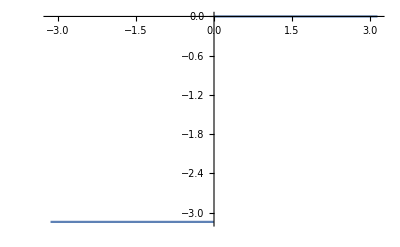

```mathematica
Plot[%13,{x1,-π,π}]
```

## Project Design

```mathematica
sol=GameSolution[..]
```

```mathematica
sol["NashEquilibrium"]
sol["MaxMin"]
sol["Stackelberg"]
```

```mathematica
sol["NashEquilibriumPlot"]
```

## Experiments with tuples for 3+ player game

----------------------------- Creating Tuples with one of strategy sets of the form {i}  ------------------------------------------------------

```mathematica
r=Tuples[{{i},Range[5],Range[5]}]
```

{{i,1,1},{i,1,2},{i,1,3},{i,1,4},{i,1,5},{i,2,1},{i,2,2},{i,2,3},{i,2,4},{i,2,5},{i,3,1},{i,3,2},{i,3,3},{i,3,4},{i,3,5},{i,4,1},{i,4,2},{i,4,3},{i,4,4},{i,4,5},{i,5,1},{i,5,2},{i,5,3},{i,5,4},{i,5,5}}

```mathematica
t=Tuples[{Range[5],{j},Range[5]}]
```

{{1,j,1},{1,j,2},{1,j,3},{1,j,4},{1,j,5},{2,j,1},{2,j,2},{2,j,3},{2,j,4},{2,j,5},{3,j,1},{3,j,2},{3,j,3},{3,j,4},{3,j,5},{4,j,1},{4,j,2},{4,j,3},{4,j,4},{4,j,5},{5,j,1},{5,j,2},{5,j,3},{5,j,4},{5,j,5}}

```mathematica
s=Tuples[{Range[5],Range[5],{k}}]
```

{{1,1,k},{1,2,k},{1,3,k},{1,4,k},{1,5,k},{2,1,k},{2,2,k},{2,3,k},{2,4,k},{2,5,k},{3,1,k},{3,2,k},{3,3,k},{3,4,k},{3,5,k},{4,1,k},{4,2,k},{4,3,k},{4,4,k},{4,5,k},{5,1,k},{5,2,k},{5,3,k},{5,4,k},{5,5,k}}

---------------------------------------------------------------- 4 player game ---------------------------------------------------------------

```mathematica
n=4;                                                                                                                                                                                        (* n - the number of players *)
```

```mathematica
listOfStrategySets=Table[Range[5],{player,n}]                                                                                        (* the list of strategy sets *)
```

{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
Clear[i];                                                                                                                                                                                (* creating the bases of the graph of best response mappings *)
Do[tuples[player]=Tuples[ReplacePart[listOfStrategySets,player->{i}]],{player,n}]
```

```mathematica
Manipulate[tuples[player],{player,1,n,1}]                                                                                                 (* visualizing the bases of the graph of best response mappings *)
```

```mathematica
Manipulate[i=j;Extract[a,tuples[1]⟦1⟧],{j,1,5,1}] (* values of payoff matrix a corresponding to tuples *)
```

-------------- First, we find the maximum for every “basic tuple”  of the graph of best response mapping -------------------------
---------------------------- Second, we compare every element of the matrix with the maxima  ----------------------------------------

```mathematica
Clear[i];
maxima=Max/@Table[Extract[a,index],{index,tuples[1]},{i,5}]; (* maximum for every "basic tuple" of the graph of best response mapping *)
graphOfBestResponseMapping[1]={};                                                                           (* graph of best response mapping *)
 k=1;
Table[If[Extract[a,index]==maxima⟦Floor[k]⟧,AppendTo[graphOfBestResponseMapping[1],index],Continue];k=k+1/5,{index,tuples[1]},{i,5}];
```

```mathematica
graphOfBestResponseMapping[1]
```

{{3,1,1,1},{4,1,1,2},{5,1,1,3},{3,1,1,4},{2,1,1,5},{1,1,2,1},{5,1,2,2},{1,1,2,3},{5,1,2,4},{3,1,2,5},{3,1,3,1},{5,1,3,1},{1,1,3,2},{4,1,3,3},{1,1,3,4},{3,1,3,4},{5,1,3,5},{4,1,4,1},{5,1,4,2},{3,1,4,3},{4,1,4,3},{3,1,4,4},{2,1,4,5},{1,1,5,1},{4,1,5,2},{1,1,5,3},{1,1,5,4},{1,1,5,5},{2,1,5,5},{1,2,1,1},{4,2,1,2},{3,2,1,3},{1,2,1,4},{5,2,1,5},{5,2,2,1},{2,2,2,2},{3,2,2,3},{2,2,2,4},{3,2,2,4},{3,2,2,5},{2,2,3,1},{4,2,3,2},{5,2,3,3},{1,2,3,4},{5,2,3,5},{3,2,4,1},{3,2,4,2},{5,2,4,3},{3,2,4,4},{1,2,4,5},{2,2,5,1},{3,2,5,2},{2,2,5,3},{3,2,5,4},{4,2,5,5},{2,3,1,1},{1,3,1,2},{5,3,1,3},{5,3,1,4},{1,3,1,5},{5,3,2,1},{2,3,2,2},{1,3,2,3},{3,3,2,3},{3,3,2,4},{5,3,2,5},{5,3,3,1},{2,3,3,2},{2,3,3,3},{1,3,3,4},{5,3,3,5},{3,3,4,1},{1,3,4,2},{2,3,4,2},{3,3,4,2},{4,3,4,3},{2,3,4,4},{2,3,4,5},{2,3,5,1},{3,3,5,1},{3,3,5,2},{1,3,5,3},{5,3,5,4},{3,3,5,5},{2,4,1,1},{1,4,1,2},{2,4,1,2},{2,4,1,3},{5,4,1,4},{5,4,1,5},{3,4,2,1},{5,4,2,2},{1,4,2,3},{4,4,2,4},{1,4,2,5},{5,4,3,1},{3,4,3,2},{3,4,3,3},{3,4,3,4},{5,4,3,4},{3,4,3,5},{1,4,4,1},{5,4,4,2},{4,4,4,3},{2,4,4,4},{4,4,4,4},{1,4,4,5},{4,4,5,1},{3,4,5,2},{1,4,5,3},{5,4,5,4},{1,4,5,5},{2,4,5,5},{2,5,1,1},{3,5,1,2},{2,5,1,3},{5,5,1,4},{2,5,1,5},{5,5,2,1},{1,5,2,2},{1,5,2,3},{5,5,2,4},{2,5,2,5},{5,5,3,1},{4,5,3,2},{3,5,3,3},{4,5,3,4},{2,5,3,5},{4,5,4,1},{1,5,4,2},{4,5,4,3},{4,5,4,4},{5,5,4,5},{3,5,5,1},{3,5,5,2},{4,5,5,3},{2,5,5,4},{2,5,5,5}}

--------------------- Plot 3D the graph of best response mapping - only for game of 3 players  ---------------------------------------

```mathematica
ListPlot3D[graphOfBestResponseMapping[1]]
```

-Graphics3D-

## Experiment with Transpose

```mathematica
Dimensions[a]
```

{5,5,5}

```mathematica
Transpose[a,{3,2,1}]//Transpose//RepeatedTiming
```

{6.×10^-6,{{{-6,1,7,5,-4},{-3,9,8,-1,5},{-3,8,-5,-8,0},{-5,-4,-9,-10,-7},{-9,7,3,-6,8}},{{-6,9,5,2,4},{8,-2,-6,4,8},{-3,-10,9,-3,5},{8,-8,-5,-6,5},{-6,-3,8,-9,-5}},{{-9,10,-7,-9,0},{-5,9,3,-2,0},{-10,-7,10,-3,-8},{8,2,-9,-1,10},{4,10,-7,8,-5}},{{-8,6,6,5,-9},{8,5,1,-1,0},{-4,3,-7,3,6},{-5,0,-8,-5,-7},{-10,4,4,-3,5}},{{-2,6,-6,8,2},{-10,-9,-2,-6,-3},{-1,-5,-1,-5,3},{-7,-10,-8,-5,-10},{0,1,3,10,3}}}}

```mathematica
{a//MatrixForm,
a-Transpose[a]⟦1⟧//MatrixForm (* subtract the 1st column from all columns *),
Transpose[Transpose[a]-a⟦1⟧] //MatrixForm(* subtract the 1st row from all rows *)}
```

{(2 | 2 | 3
3 | 2 | 1
1 | 3 | 3),(0 | 0 | 1
0 | -1 | -2
0 | 2 | 2),(0 | 0 | 0
1 | 0 | -2
-1 | 1 | 0)}

## Stackelberg Equilibrium

```mathematica
t=Tuples[{Range[3],Range[2],Range[2],Range[3],{𝕚}}]
```

{{1,1,1,1,𝕚},{1,1,1,2,𝕚},{1,1,1,3,𝕚},{1,1,2,1,𝕚},{1,1,2,2,𝕚},{1,1,2,3,𝕚},{1,2,1,1,𝕚},{1,2,1,2,𝕚},{1,2,1,3,𝕚},{1,2,2,1,𝕚},{1,2,2,2,𝕚},{1,2,2,3,𝕚},{2,1,1,1,𝕚},{2,1,1,2,𝕚},{2,1,1,3,𝕚},{2,1,2,1,𝕚},{2,1,2,2,𝕚},{2,1,2,3,𝕚},{2,2,1,1,𝕚},{2,2,1,2,𝕚},{2,2,1,3,𝕚},{2,2,2,1,𝕚},{2,2,2,2,𝕚},{2,2,2,3,𝕚},{3,1,1,1,𝕚},{3,1,1,2,𝕚},{3,1,1,3,𝕚},{3,1,2,1,𝕚},{3,1,2,2,𝕚},{3,1,2,3,𝕚},{3,2,1,1,𝕚},{3,2,1,2,𝕚},{3,2,1,3,𝕚},{3,2,2,1,𝕚},{3,2,2,2,𝕚},{3,2,2,3,𝕚}}

```mathematica
l=t/.𝕚:>RandomInteger[3]
```

{{1,1,1,1,1},{1,1,1,2,2},{1,1,1,3,3},{1,1,2,1,2},{1,1,2,2,0},{1,1,2,3,2},{1,2,1,1,0},{1,2,1,2,1},{1,2,1,3,2},{1,2,2,1,2},{1,2,2,2,0},{1,2,2,3,1},{2,1,1,1,3},{2,1,1,2,3},{2,1,1,3,2},{2,1,2,1,2},{2,1,2,2,3},{2,1,2,3,2},{2,2,1,1,1},{2,2,1,2,2},{2,2,1,3,0},{2,2,2,1,1},{2,2,2,2,1},{2,2,2,3,3},{3,1,1,1,0},{3,1,1,2,2},{3,1,1,3,0},{3,1,2,1,2},{3,1,2,2,2},{3,1,2,3,0},{3,2,1,1,2},{3,2,1,2,1},{3,2,1,3,0},{3,2,2,1,2},{3,2,2,2,0},{3,2,2,3,2}}

```mathematica
maxPositions[list_]:=Pick[Range@Length@list, list,Max[list]]
```

```mathematica
Dimensions[l][[2]]
```

{36,5}

```mathematica
GatherBy[l,Take[#,Dimensions[l]⟦2⟧-2]&]
```

{{{1,1,1,1,1},{1,1,1,2,2},{1,1,1,3,3}},{{1,1,2,1,2},{1,1,2,2,0},{1,1,2,3,2}},{{1,2,1,1,0},{1,2,1,2,1},{1,2,1,3,2}},{{1,2,2,1,2},{1,2,2,2,0},{1,2,2,3,1}},{{2,1,1,1,3},{2,1,1,2,3},{2,1,1,3,2}},{{2,1,2,1,2},{2,1,2,2,3},{2,1,2,3,2}},{{2,2,1,1,1},{2,2,1,2,2},{2,2,1,3,0}},{{2,2,2,1,1},{2,2,2,2,1},{2,2,2,3,3}},{{3,1,1,1,0},{3,1,1,2,2},{3,1,1,3,0}},{{3,1,2,1,2},{3,1,2,2,2},{3,1,2,3,0}},{{3,2,1,1,2},{3,2,1,2,1},{3,2,1,3,0}},{{3,2,2,1,2},{3,2,2,2,0},{3,2,2,3,2}}}

```mathematica
s=GatherBy[l,Last]
```

```mathematica
Apply[a[[#]]&,{{{1,1,1,1,1},{1,2,1,2,1},{1,2,2,3,1},{2,2,1,1,1},{2,2,2,1,1},{2,2,2,2,1},{3,2,1,2,1}},{{1,1,1,2,2},{1,1,2,1,2},{1,1,2,3,2},{1,2,1,3,2},{1,2,2,1,2},{2,1,1,3,2},{2,1,2,1,2},{2,1,2,3,2},{2,2,1,2,2},{3,1,1,2,2},{3,1,2,1,2},{3,1,2,2,2},{3,2,1,1,2},{3,2,2,1,2},{3,2,2,3,2}},{{1,1,1,3,3},{2,1,1,1,3},{2,1,1,2,3},{2,1,2,2,3},{2,2,2,3,3}},{{1,1,2,2,0},{1,2,1,1,0},{1,2,2,2,0},{2,2,1,3,0},{3,1,1,1,0},{3,1,1,3,0},{3,1,2,3,0},{3,2,1,3,0},{3,2,2,2,0}}},{2}]
```

```mathematica
s[[1,1]]
```

{1,1,1,1,1}

```mathematica
a[[1,1,1,1,1]]
```

493

```mathematica
a⟦Sequence@@s⟦1,1⟧⟧
```

493

```mathematica
s[[1,1]]
```

{1,1,1,1,1}

```mathematica
Dimensions[a]
```

{5,5,5,5,5}

```mathematica
Tuples[Table[Range[Dimensions[a][[i]]],{i,Length[Dimensions[a]]}]]
```

{{1,1,1,1,1},{1,1,1,1,2},{1,1,1,1,3},{1,1,1,1,4},{1,1,1,1,5},{1,1,1,2,1},{1,1,1,2,2},{1,1,1,2,3},{1,1,1,2,4},{1,1,1,2,5},{1,1,1,3,1},{1,1,1,3,2},{1,1,1,3,3},{1,1,1,3,4},{1,1,1,3,5},{1,1,1,4,1},{1,1,1,4,2},{1,1,1,4,3},{1,1,1,4,4},{1,1,1,4,5},{1,1,1,5,1},{1,1,1,5,2},{1,1,1,5,3},{1,1,1,5,4},{1,1,1,5,5},{1,1,2,1,1},{1,1,2,1,2},3072,{5,5,4,5,5},{5,5,5,1,1},{5,5,5,1,2},{5,5,5,1,3},{5,5,5,1,4},{5,5,5,1,5},{5,5,5,2,1},{5,5,5,2,2},{5,5,5,2,3},{5,5,5,2,4},{5,5,5,2,5},{5,5,5,3,1},{5,5,5,3,2},{5,5,5,3,3},{5,5,5,3,4},{5,5,5,3,5},{5,5,5,4,1},{5,5,5,4,2},{5,5,5,4,3},{5,5,5,4,4},{5,5,5,4,5},{5,5,5,5,1},{5,5,5,5,2},{5,5,5,5,3},{5,5,5,5,4},{5,5,5,5,5}}
 |  |  |  |

## Settings

```mathematica
?GameTheory
```

```mathematica
??GameTheory
```

```mathematica
$Packages
```

```mathematica
SetOptions[EvaluationNotebook[],WindowTitle-> "GT Project"]
```

```mathematica
SeedRandom[1](* Posibilitatea de a seta ca sa se genereze aceasi numere aleatoare repetat *)
```